# Figure 1

```mathematica
H[q_,p_,gg_]=(q^2+p^2)/2-(1/2)*(1+(Sqrt[2]*gg*q)^2)^(1/2);
V[q_,gg_]=q^2/2-(1/2)*(1+(Sqrt[2]*gg*q)^2)^(1/2);
```

#### First column

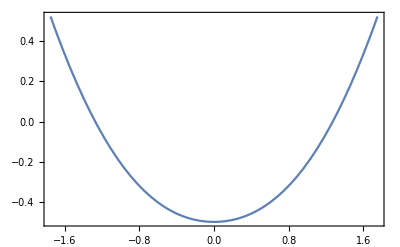

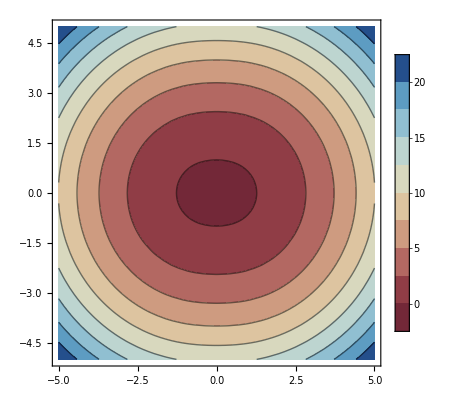

```mathematica
g=1/2^(1/2);
pot=Show[Plot[V[q,g],{q,-1.75,1.75},Frame->True,Axes->False,LabelStyle->{Black,15}],Plot[{},{x,-1.75,1.75},PlotStyle->{{Dashed,Gray}}]]

contour=ContourPlot[H[q,p,g],{q,-5,5},{p,-5,5},PlotLegends->Automatic,LabelStyle->{22,Black},ColorFunction->"RedBlueTones"]
```

#### Second column

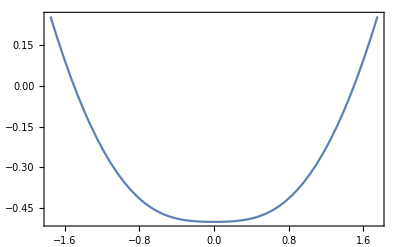

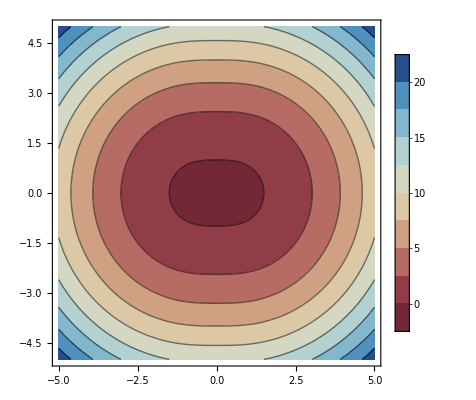

```mathematica
g=0.95;
pot=Show[Plot[V[q,g],{q,-1.75,1.75},Frame->True,Axes->False,LabelStyle->{Black,15}],Plot[{},{x,-1.75,1.75},PlotStyle->{{Dashed,Gray}}]]

contour=ContourPlot[H[q,p,g],{q,-5,5},{p,-5,5},PlotLegends->Automatic,LabelStyle->{22,Black},ColorFunction->"RedBlueTones"]
```

#### Third column

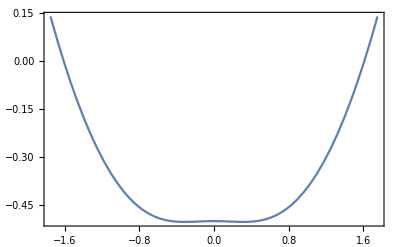

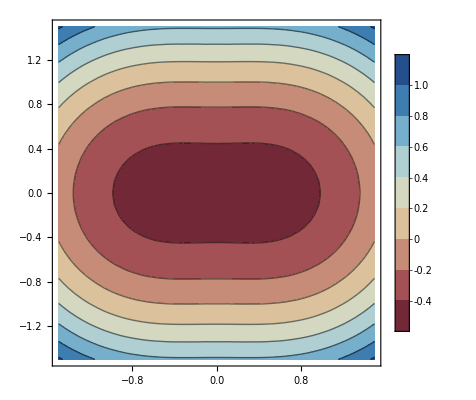

```mathematica
g=1.05;
pot=Show[Plot[V[q,g],{q,-1.75,1.75},Frame->True,Axes->False,LabelStyle->{Black,15}],Plot[{},{x,-1.75,1.75},PlotStyle->{{Dashed,Gray}}]]

contour=ContourPlot[H[q,p,g],{q,-1.5,1.5},{p,-1.5,1.5},PlotLegends->Automatic,LabelStyle->{22,Black},ColorFunction->"RedBlueTones"]
```

#### Fourth column

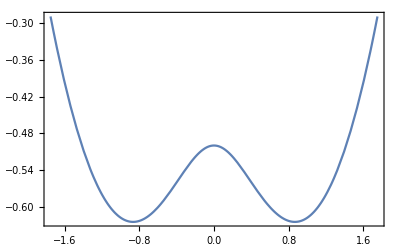

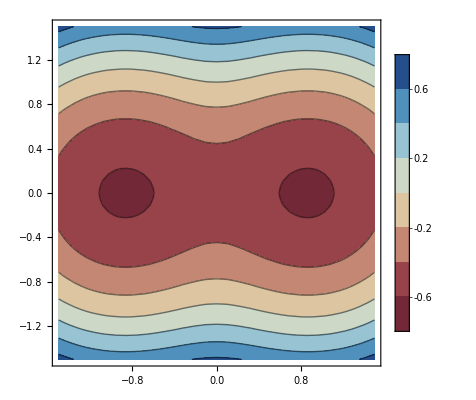

```mathematica
g=2^(1/2);
pot=Show[Plot[V[q,g],{q,-1.75,1.75},Frame->True,Axes->False,LabelStyle->{Black,15}],Plot[{},{x,-1.75,1.75},PlotStyle->{{Dashed,Gray}}]]

contour=ContourPlot[H[q,p,g],{q,-1.5,1.5},{p,-1.5,1.5},PlotLegends->Automatic,LabelStyle->{22,Black},ColorFunction->"RedBlueTones"]
```